Coherence properties

Speckle size: 0.00169341/w0 μm

Cross over distance zvcz: 0.00031831/w0 cm

Fraunhofer distance zfr: 1.8797 m

Deep Fresnel zone, z << Crossover distance

Gaussian profile speckle

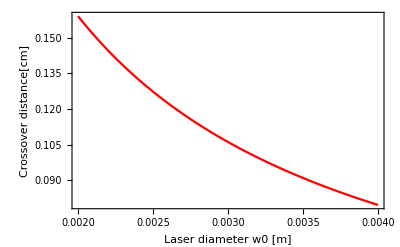

Longitudinal size (= Rayleigh range)

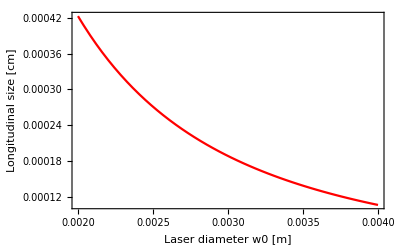

Tranverse size

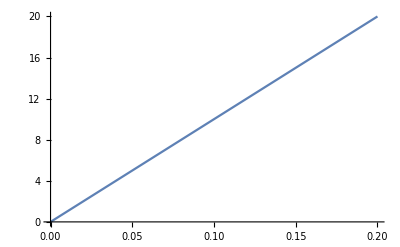

1.69341 μm

```mathematica
Print[Style["Coherence properties" ,20]]
(* Important distances: 
Cross over distance: zvcz 
Fraunhofer distance of the source: zfr *)
λ = 632.8 *10^(-9);(*Wavelength of the source*) 
λ = 532*10^(-9);(*Wavelength of the source*) 
(*w0=3.2*10^(-3); (* Diameter of the laser beam on the diffuser*)*)
F= 10*10^(-3); (* Focal length of the far field lens*)

Diam= 5*10^(-3) ;   (*Transverse size of the source (aperture diameter)*) 
δx0 = N[λ*F/(Pi*w0)]; (* Dimension of the speckle at source plane *)
Print["Speckle size: ", δx0 *10^(6), " μm"]
Print[""]
zvcz = N[Diam * δx0 /λ ];
Print["Cross over distance zvcz: ", zvcz *10^(2), " cm"]
Print[""]
zfr = N[Diam^2/λ];
Print["Fraunhofer distance zfr: ", zfr , " m"]
Print[""]
Print[Style["Deep Fresnel zone, z << Crossover distance", 18,Red]]

Print [Style["Gaussian profile speckle",18, Red]]

zd=N[Pi*δx0^2/λ] ; (*Rayleigh range*)

Plot[N[zvcz]*10^2,{w0,2*10^(-3),4*10^(-3)}, Frame->True, PlotStyle->Red,BaseStyle->{FontFamily->"Helvetica",20}, FrameLabel->{"Laser diameter w0 [m]","Crossover distance[cm]"}]
GδznDFZ =  zd; (*Longitudinal size *)
Print[Style["Longitudinal size (= Rayleigh range)",18, Red]]
Plot[N[GδznDFZ]*10^2,{w0,2*10^(-3),4*10^(-3)}, Frame->True, PlotStyle->Red,BaseStyle->{FontFamily->"Helvetica",20}, FrameLabel->{"Laser diameter w0 [m]","Longitudinal size [cm]"}]


GδxnDFZ = N[δx0 *Sqrt[1+(dz/zd)^2]];    (* Tranverse size; dz is the different path of a splitted speckle pattern*) 

WaistEvolutionTr = N[Waist0 *Sqrt[1+(dz/(Pi*Waist0 ^2/λ))^2]];    (* Tranverse size; dz is the different path of a splitted speckle pattern*) 

Print[Style["Tranverse size" ,18, Red]]

Manipulate[Plot[(Pi*λ*F/w0*Sqrt[1+(dz/Pi*(Pi*λ*F/w0)^2/λ)])*10^6,{dz,0.001,0.1 }, PlotStyle->Red,BaseStyle->{FontFamily->"Helvetica",20}, FrameLabel->{"Path difference[m]","Speckle size [μm]"},Frame->True],{{w0,3*10^(-3)},10^(-3),10^(-1)}]

Plot[(GδxnDFZ  *10^3) /. {w0  ->1*10^(-3)}, {dz, 0, 200 10^(-3)}]
Print[Style[10^6*δx0/. {w0  ->1*10^(-3)} ,20],Style[" μm ",20]]
```

```mathematica
Print[Style["Parameter for the setup: w0 = 2 mm" ,18, Red]]

Print[Style["Rayleight distance: zd = " ,18, Red], Style[10^(2)*zd/.{w0->0.0012},18, Red], Style[" cm" ,18, Red] ]

Print[Style["Cross over distance: zvcz = " ,18, Red], Style[10^(2)*zvcz/.{w0->0.0012},18, Red], Style[" cm" ,18, Red] ]
```

Parameter for the setup: w0 = 2 mm

Rayleight distance: zd = 0.00117598 cm

Cross over distance: zvcz = 0.265258 cm

```mathematica
Print[Style["Beam reduction" ,20]]
w0In= 4*10^(-3);
w0Out = 2*10^(-3);
M= w0Out /w0In;

F1= M*F2
L=N[F1+F2]
```

Beam reduction

F2/2

1.5 F2

```mathematica
(*Planar quasi homogeneous source*)
(* Deep Fresnel zone z<<zvcz *) 
δxnDFZ = N[δx0  ]     (* Tranverse size *) ;
δznDFZ =  N[δxnDFZ^2/λ]   (*Longitudinal size *) ;
(* Fresnel zone (VCZ zone?) zvcz < z < zfr *) 

δxnFZ = N[λ z /Diam ];     (* Tranverse size *) 
δznFZ =  N[δxnFZ^2/λ*(1/(1-z/zfr)) ];(*Longitudinal size *) 

Print["VCZ zone ", zvcz, "< z < ", zfr]
```

VCZ zone (3.1831×10^-6)/w0< z < 1.8797

```mathematica
Plot[δznFZ,{z,zvcz,zfr}]
```

Plot::plln: Limiting value (3.1831×10^-6)/w0 in {z,(3.1831×10^-6)/w0,1.8797} is not a machine-sized real number.

Plot[δznFZ,{z,zvcz,zfr}]

```mathematica
z1= 0.110 
δznFZ1=δznFZ/.{z->z1}
```

0.11

0.00683732